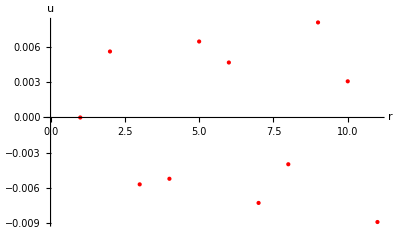

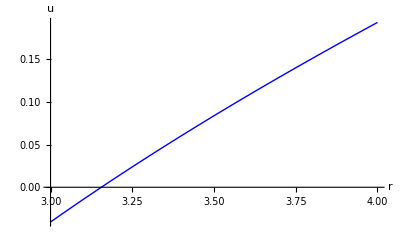

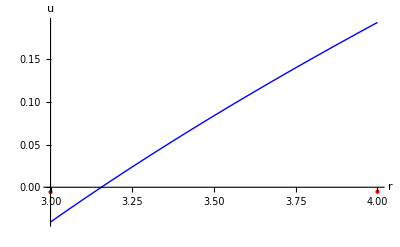

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
numSolution=ReadList["axis.txt", Number];
settings = ReadList["axisSettings.txt",Number];
h =settings[[1]];a =settings[[2]];b =settings[[3]];
Pa =settings[[4]];Pb=settings[[5]];e=settings[[6]];
nu=settings[[7]];
exactSol[r_]:= (1-nu)(1+2nu)/e*(Pa a^2-Pb b^2)/(a^2-b^2)r+(1 + nu)/e * (a^2 b^2)/r * (Pa -Pb)/(b^2-a^2);
plot = ListPlot[numSolution, PlotStyle->{Red},PlotTheme->"Classic",AxesLabel->{r,u}]
plot1 =Plot[exactSol[r],{r, a,b},PlotTheme->"Classic",AxesLabel->{r,u},PlotStyle->{Thick, Blue}]
k=Show[plot1, plot]
(*Export["ff.pdf",k]*)
```

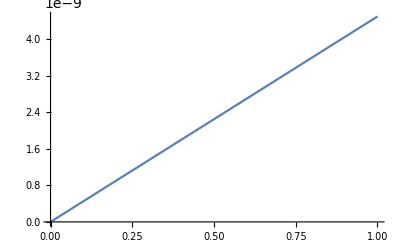

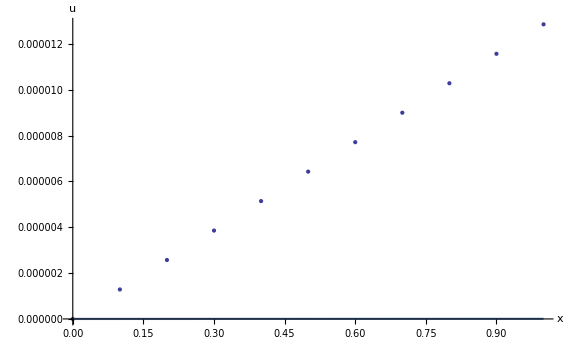

```mathematica
Y=Import["kvasiOut.txt", "Data"];(*For Solutions*)
h = Y[[1]][[1]];
tau = Y[[2]][[1]];
time = {};data={};
m= Length[Y];
P[t_]:=p*t;
kvasiExactSol[x_,t_]:=P[t] /e* x;
n =Length[Y[[1]]];
For[i =0 ,i <5,i++,
num =  Round[m/5* i + 3];
data=Append[data,Table[{h*(k-1),Y[[num]][[k]]},{k,1,n}]];
tt=tau*(num - 3);
t=StringJoin["t = ",ToString[tt]];
time= Append[time,t];
];
pl =ListPlot[data,AxesLabel->{"x","u"},PlotTheme->"Classic",PlotRange->All,PlotLegends->time, ImageSize->Large];
p1 =ListPlot[data[[5]],AxesLabel->{"x","u"},PlotTheme->"Classic",PlotRange->All,PlotLegends->time[[5]], ImageSize->Large];
p2=Plot[kvasiExactSol[x,0.9],{x,0,1}]
Show[p1,p2]
```

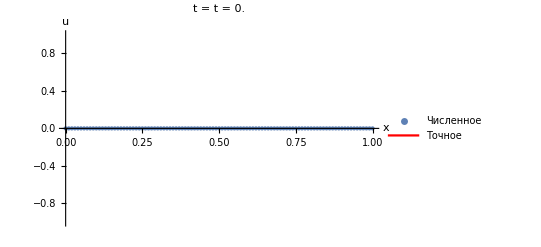

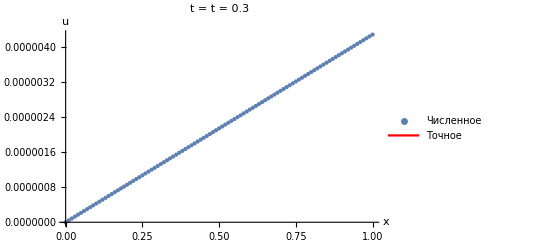

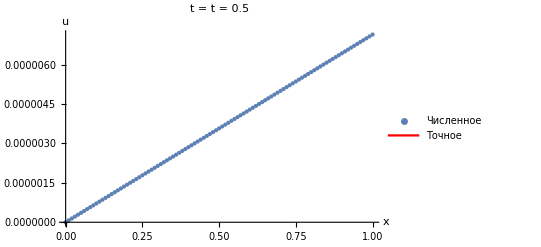

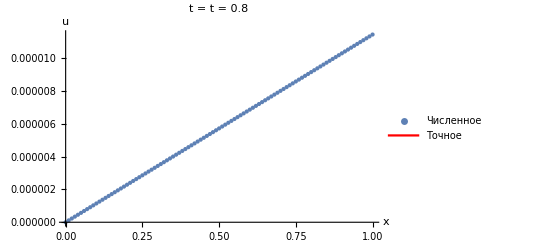

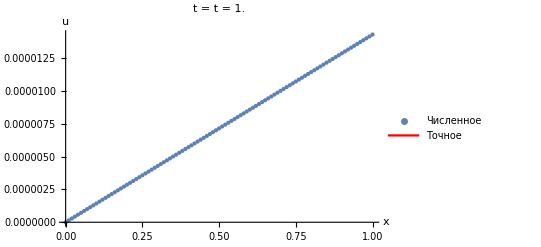

```mathematica
maxError=0;
For[i =0 ,i <5,i++,
error =Max[Table[{N[data[[i+1]][[k]][[2]] - kvasiExactSol[data[[i+1]][[k]][[1]] ,time[[i+1]]]]},{k,1,n}]];
maxError=Max[{error, maxError}];
Show[ListPlot[data[[i + 1]],AxesLabel->{"x","u"},AxesStyle->Thick,LabelStyle->Directive[20],PlotLabel->Style[StringJoin[StringJoin["t = ",ToString[time[[i + 1]]]],""]],PlotStyle->PointSize[Medium],PlotRange->All,PlotLegends->{"Численное"}],
Plot[kvasiExactSol[x,time[[i+1]]],{x, 0,1.0},PlotStyle->Red,PlotLegends->{"Точное"},AxesStyle->Thick,LabelStyle->Directive[20]]]//Print
];
```

```mathematica
|
```

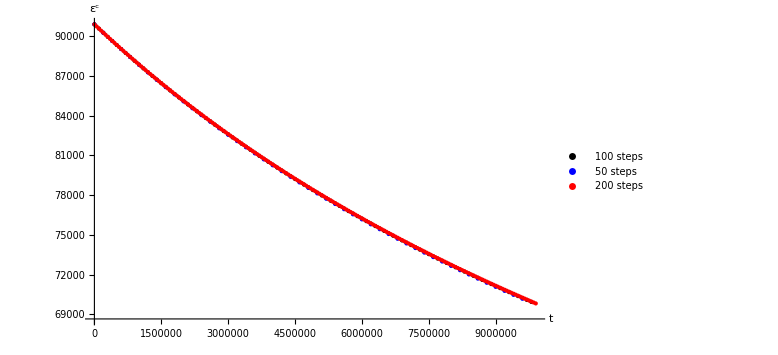

12.pdf

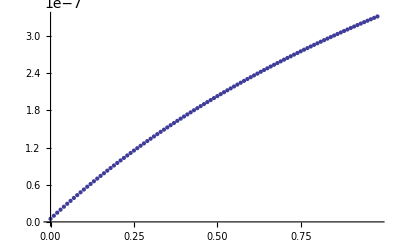

-Graphics-

```mathematica
AA=Import["sigma.txt", "Data"];(*For Sigma*)
time1= {};data1={};
m= Length[AA];
h = AA[[1]][[1]];
tau = AA[[2]][[1]];
n =Length[AA[[1]]];
For[i =3,i <Length[AA],i++,
data1=Append[data1,{tau*(i-3),AA[[i]][[1]]}];
];
AA=Import["sigma1.txt", "Data"];
time1= {};data2={};
m= Length[AA];
h = AA[[1]][[1]];
tau = AA[[2]][[1]];
n =Length[AA[[1]]];
For[i =3,i <Length[AA],i++,
data2=Append[data2,{tau*(i-3),AA[[i]][[1]]}];
];
AA=Import["sigma2.txt", "Data"];
time1= {};data3={};
m= Length[AA];
h = AA[[1]][[1]];
tau = AA[[2]][[1]];
n =Length[AA[[1]]];
For[i =3,i <Length[AA],i++,
data3=Append[data3,{tau*(i-3),AA[[i]][[1]]}];
];

plqw =ListPlot[{data1, data2, data3},PlotTheme->"Classic",AxesLabel->{"t",ε^c},PlotStyle->{{Black,PointSize[Medium]}, {Blue, PointSize[Large]}, {Red, PointSize[Small]}}, ImageSize->Large, PlotLegends->{"100 steps","50 steps","200 steps"}]
Export["12.pdf",plqw]
```